# NLS universality class

```mathematica
Quit[];
```

## Focusing NLS - Code by Tom Trogdon

```mathematica
θ[k_,x_,t_]:=2k x+2k^2t;
cc[x_]:=Conjugate[x];
Cs[x_,t_]:=Table[cs[[i]] Exp[I θ[ks[[i]],x,t]],{i,1,Length[ks]}];
iii[x_,t_]:=(Abs[#]>1)&/@Cs[x//N,t//N];
ii[x_,t_]:=Module[{out={},out2={},data,j},
data = iii[x,t];
For[j=1,j≤Length[data],j++,
If[
data[[j]], AppendTo[out,j],AppendTo[out2,j]
];
];
{out,out2}
];
H11[x_,t_]:=Module[{h=ConstantArray[0,{Length[ks],Length[ks]}],is,isc,i,j,l,k},
{is,isc} = ii[x,t];
For[k=1,k≤Length[isc],k++,
i=isc[[k]];
For[l=1,l≤Length[is],l++,
j=is[[l]];
h[[i,j]]=1/(ks[[i]]-ks[[j]]);
];
];

For[k=1,k≤Length[is],k++,
i=is[[k]];
For[l=1,l≤Length[isc],l++,
j=isc[[l]];
h[[i,j]]=1/(ks[[i]]-ks[[j]]);
];
];
h
];
H22[x_,t_]:=Module[{h=ConstantArray[0,{Length[ks],Length[ks]}],is,isc,i,j,l,k},
{is,isc} = ii[x,t];
For[k=1,k≤Length[isc],k++,
i=isc[[k]];
For[l=1,l≤Length[is],l++,
j=is[[l]];
h[[i,j]]=1/(ks[[i]]-ks[[j]])//cc;
];
];

For[k=1,k≤Length[is],k++,
i=is[[k]];
For[l=1,l≤Length[isc],l++,
j=isc[[l]];
h[[i,j]]=1/(ks[[i]]-ks[[j]])//cc;
];
];
h
];
H12[x_,t_]:=Module[{h=ConstantArray[0,{Length[ks],Length[ks]}],is,isc,i,j,l,k},
{is,isc} = ii[x,t];
For[k=1,k≤Length[isc],k++,
i=isc[[k]];
For[l=1,l≤Length[isc],l++,
j=isc[[l]];
h[[i,j]]=1/(ks[[i]]-cc[ks[[j]]]);
];
];

For[k=1,k≤Length[is],k++,
i=is[[k]];
For[l=1,l≤Length[is],l++,
j=is[[l]];
h[[i,j]]=1/(ks[[i]]-cc[ks[[j]]]);
];
];
h
];
H21[x_,t_]:=Module[{h=ConstantArray[0,{Length[ks],Length[ks]}],is,isc,i,j,l,k},
{is,isc} = ii[x,t];
For[k=1,k≤Length[isc],k++,
i=isc[[k]];
For[l=1,l≤Length[isc],l++,
j=isc[[l]];
h[[i,j]]=1/(cc[ks[[i]]]-ks[[j]]);
];
];

For[k=1,k≤Length[is],k++,
i=is[[k]];
For[l=1,l≤Length[is],l++,
j=is[[l]];
h[[i,j]]=1/(cc[ks[[i]]]-ks[[j]]);
];
];
h
];
q[k_,x_,t_]:=Module[{out,is,isc,j},
{is,isc} = ii[x,t];
Product[(k-ks[[is[[j]]]])/(k-cc[ks[[is[[j]]]]]),
{j,1,Length[is]}]
];
quhp[k_,x_,t_,l_]:=Module[{out,is,isc,j},
{is,isc} = ii[x,t];
Product[
If[l≠is[[j]],(k-ks[[is[[j]]]])/(k-cc[ks[[is[[j]]]]]),1/(k-cc[ks[[is[[j]]]]])],
{j,1,Length[is]}]
];
qlhp[k_,x_,t_,l_]:=Module[{out,is,isc,j},
{is,isc} = ii[x,t];
Product[
If[l≠is[[j]],(k-ks[[is[[j]]]])/(k-cc[ks[[is[[j]]]]]),(k-ks[[is[[j]]]])],
{j,1,Length[is]}]
];
diag1[x_,t_]:=Module[{out=ConstantArray[0,Length[ks]],is,isc,i,Cexp,k},
{is,isc} = ii[x,t];
Cexp=Cs[x,t];
For[k=1,k≤Length[isc],k++,
i=isc[[k]];
out[[i]]=q[ks[[i]],x,t]^2*Cexp[[i]];
];
For[k=1,k≤Length[is],k++,
i=is[[k]];
out[[i]]=1/(quhp[ks[[i]],x,t,i]^(2)*Cexp[[i]]);
];
out];
diag2[x_,t_]:=Module[{out=ConstantArray[0,Length[ks]],is,isc,i,Cexp,k},
{is,isc} = ii[x,t];
Cexp=Cs[x,t];
For[k=1,k≤Length[isc],k++,
i=isc[[k]];
out[[i]]=-q[ks[[i]]//cc,x,t]^(-2)*cc[Cexp[[i]]];
];
For[k=1,k≤Length[is],k++,
i=is[[k]];
out[[i]]=-qlhp[ks[[i]]//cc,x,t,i]^(2)/(cc[Cexp[[i]]]);
];
out];
LS[x_,t_]:=Module[{A,b,diags1,diags2,Ax,b1,b2,is,isc,k,i,H},
diags1=diag1[x,t];
diags2=diag2[x,t];
(*b1 = ConstantArray[0,Length[ks]];b2=b1;
{is,isc} = ii[x,t];
For[k=1,k≤Length[isc],k++,
i=isc[[k]];
b2[[i]]=diags2[[i]];
];
For[k=1,k≤Length[is],k++,
i=is[[k]];
b1[[i]]=diags1[[i]];
];
b = Join[b1,b2];*)

b1 = ConstantArray[0,Length[ks]];b2=b1;
{is,isc} = ii[x,t];
For[k=1,k≤Length[isc],k++,
i=isc[[k]];
b2[[i]]=1;
];
For[k=1,k≤Length[is],k++,
i=is[[k]];
b1[[i]]=1;
];
b = Join[b1,b2];

H=Join[Join[H11[x,t],H12[x,t],2],Join[H21[x,t],H22[x,t],2]];
A=IdentityMatrix[2Length[ks]]-DiagonalMatrix[Join[diags1,diags2]].H;
{A,DiagonalMatrix[Join[diags1,diags2]].b}
];
sol[x_,t_]:=Module[{A,b,Ax,bx,u,ux,u1,u2,sum,k,i,isc,is},
{A,b}=LS[x,t];
u=LinearSolve[A,b];
u2=u[[Length[ks]+1;;]];
u1=u[[1;;Length[ks]]];
sum = 0;
{is,isc} = ii[x,t];
For[k=1,k≤Length[isc],k++,
i=isc[[k]];
sum = sum + u2[[i]];
];
For[k=1,k≤Length[is],k++,
i=is[[k]];
sum = sum + u1[[i]];
];
2I sum
];
```

## High precision

```mathematica
sp[x_]:=SetPrecision[x,600]; (* Set code precision to 300 digits*)
```

### PIII - initial data

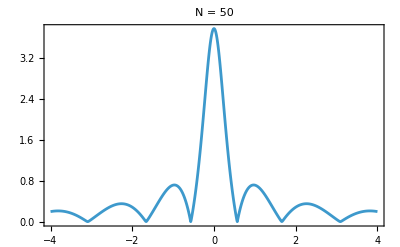

Exported: C:\Users\MazzucaGuido\Documents\GitHub\RogueWaveInfiniteNLS.jl\src\50solitonPIII.csv

$Aborted

```mathematica
(*1. Define the Parameter for the Chi Distribution*)
nu=4; 

(*2. Define the analytical mean of the Chi Distribution for muD*)
(*Mean of Chi(nu)=Sqrt[2]*Gamma((nu+1)/2)/Gamma(nu/2)*)
muDCalculated=Sqrt[2]*Gamma[(nu+1)/2]/Gamma[nu/2];

(*4. Loop over the requested Soliton numbers:50,100,200*)
solitonCounts={50,100,200};

Do[(*---A.Setup Parameters for this Iteration---*)
Nsoliton=currentN;
muD=muDCalculated;
(*---B.Generate Random ks---*)
ks=Table[RandomVariate[NormalDistribution[0,15]]+I*RandomVariate[ChiDistribution[nu]],{i,1,Nsoliton}]//sp;
(*---C.Calculate Norming Constants (cs)---*)
cs=Table[Product[ks[[j]]-cc[ks[[n]]],{n,1,Length[ks]}]/Product[ks[[j]]-ks[[n]],{n,1,j-1}]/Product[ks[[j]]-ks[[n]],{n,j+1,Length[ks]}],{j,1,Length[ks]}];
(*---D.Generate Data---*)
data=ParallelTable[{xx,Abs[2/(Nsoliton muD)*sol[(2 xx)/(Nsoliton muD),0]]},{xx,-4,4,1/100}];
(*---E.Plotting (Optional:to see progress)---*)
printPlot=ListPlot[data,Joined->True,PlotRange->All,Axes->False,Frame->True,PlotLabel->Row[{"N = ",Nsoliton}]];
Print[printPlot];
(*---F.Export to CSV---*)
fileName=ToString[Nsoliton]<>"solitonPIII.csv";
path=FileNameJoin[{NotebookDirectory[],fileName}];
Export[path,data];
Print["Exported: ",path];,{currentN,solitonCounts} (*End of Do Loop*)];
```

### PV - Initial data

0.3

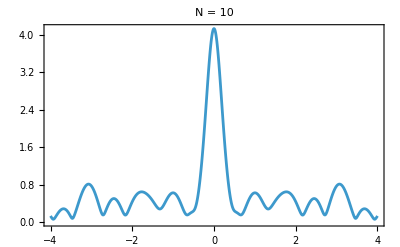

Exported: C:\Users\MazzucaGuido\Documents\GitHub\RogueWaveInfiniteNLS.jl\src\10solitonPV.csv

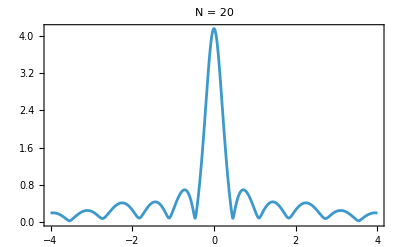

Exported: C:\Users\MazzucaGuido\Documents\GitHub\RogueWaveInfiniteNLS.jl\src\20solitonPV.csv

```mathematica
(*1. Define the Parameter for the Chi Distribution and zeta*)
nu=4; 
ζ=0.3
(*2. Define the analytical mean of the Chi Distribution for muD*)
(*Mean of Chi(nu)=Sqrt[2]*Gamma((nu+1)/2)/Gamma(nu/2)*)
muDCalculated=Sqrt[2]*Gamma[(nu+1)/2]/Gamma[nu/2];

(*4. Loop over the requested Soliton numbers:50,100,200*)
solitonCounts={50,100,200};

Do[(*---A.Setup Parameters for this Iteration---*)
Nsoliton=currentN;
muD=muDCalculated;
(*---B.Generate Random ks---*)
ks=Table[RandomVariate[NormalDistribution[0,15]]+ζ *i +I*RandomVariate[ChiDistribution[nu]],{i,1,Nsoliton}]//sp;
(*---C.Calculate Norming Constants (cs)---*)
cs=Table[Product[ks[[j]]-cc[ks[[n]]],{n,1,Length[ks]}]/Product[ks[[j]]-ks[[n]],{n,1,j-1}]/Product[ks[[j]]-ks[[n]],{n,j+1,Length[ks]}],{j,1,Length[ks]}];
(*---D.Generate Data---*)
data=ParallelTable[{xx,Abs[2/(Nsoliton muD)*sol[(2 xx)/(Nsoliton muD),0]]},{xx,-4,4,1/100}];
(*---E.Plotting (Optional:to see progress)---*)
printPlot=ListPlot[data,Joined->True,PlotRange->All,Axes->False,Frame->True,PlotLabel->Row[{"N = ",Nsoliton}]];
Print[printPlot];
(*---F.Export to CSV---*)
fileName=ToString[Nsoliton]<>"solitonPV.csv";
path=FileNameJoin[{NotebookDirectory[],fileName}];
Export[path,data];
Print["Exported: ",path];,{currentN,solitonCounts} (*End of Do Loop*)];
```